```mathematica
ClearAll["Global*'"]
```

```mathematica
Tlist={0.00001, 0.0000158489 ,0.0000251189, 0.0000398107, 0.0000630957, 0.0001 ,0.0001584893, 0.0002511886, 0.0003981072 ,0.00063095730,.001, 0.00158489 ,0.00251189 ,0.00398107 ,0.00630957 ,0.01, 0.01584893, 0.02511886, 0.03981072, 0.06309573 ,0.1,0.11, 0.12 ,0.13, 0.14 ,0.15};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.00001000,0.00001585,0.00002512,0.00003981,0.00006310,0.00010000,0.00015849,0.00025119,0.00039811,0.00063096,0.00100000,0.00158489,0.00251189,0.00398107,0.00630957,0.01000000,0.01584893,0.02511886,0.03981072,0.06309573,0.10000000,0.11000000,0.12000000,0.13000000,0.14000000,0.15000000}

```mathematica
plist={3.70, 3.72 ,3.74 ,3.76 ,3.78, 3.80};
pstring=ToString[NumberForm[#,{5,3},ExponentFunction->(Null&)]]&/@plist
```

{3.700,3.720,3.740,3.760,3.780,3.800}

```mathematica
datasets=Table[Table[Import[StringJoin["/Users/chengling/Learning/Research/G_T/cellGPU/testData/preliminary_N900_p",pstring[[p]],"_T",Tstring[[T]],"_time5000000.nc"],"Data"],{T,Length[Tstring]}],{p,Length[pstring]}];
```

```mathematica
data=Import["/Users/chengling/Learning/Research/G_T/cellGPU/testData/preliminary_N900_p3.740_T0.00158489_time5000000.nc","Datasets"]
```

{/BoxMatrix,/d2Edgammadgamma,/energy,/sigma}

```mathematica
|
```

```mathematica
area=datasets[[1,1]][[1,1]][[4]]*datasets[[1,1]][[1,1]][[4]];
```

```mathematica
p380=Table[1/area ()]
```

```mathematica
datasets[[6,9]][[4,4999]][[1]]
```

-0.00200536

```mathematica
Gp=Table[Table[Table[datasets[[p,T]][[2,i]][[1]],{i,10001,50000}],{T,Length[Tstring]}],{p,Length[pstring]}];
```

```mathematica
Sigmap=Table[Table[Table[datasets[[p,T]][[4,i]][[1]]*area,{i,10001,50000}],{T,Length[Tstring]}],{p,Length[pstring]}];
```

```mathematica
varsig=Table[Table[Variance[Sigmap[[p,T]]],{T,Length[Tstring]}],{p,Length[pstring]}];
```

```mathematica
meanG=Table[Table[Mean[Gp[[p,T]]],{T,Length[Tstring]}],{p,Length[pstring]}];
```

```mathematica
G=Table[Table[1/area*(meanG[[p,i]]-varsig[[p,i]]/Tlist[[i]]),{i,Length[Tlist]}],{p,Length[pstring]}]
```

{{0.345225,0.310078,0.192118,0.294356,0.275041,-0.0120113,0.247144,0.236787,0.234372,0.213333,0.153196,0.173576,0.0759961,-0.493009,0.132028,0.104641,0.208159,0.0296451,0.0778676,0.157693,-2.13967×10^6,0.275118,-2830.35,-4580.55,0.322544,-2674.78},{0.23662,0.266336,0.267284,0.246604,0.228889,0.232318,0.204787,0.181541,0.167578,0.149844,0.127199,0.0659617,-0.00523916,0.0804926,0.125539,0.160319,-0.0514819,0.0467962,0.0846578,0.165561,-0.0428393,-173.978,-204.554,-105.145,-53.1969,-4.93266},{0.236969,0.235525,0.203643,0.19815,0.170545,0.172134,0.150938,0.142799,0.116332,0.0176534,0.0713412,-0.0903415,0.0426996,-0.210705,0.102778,0.132254,0.0261373,0.0527381,0.0986215,0.155887,0.26415,-0.331877,0.0235786,-27.5839,0.0405792,-54048.9},{0.00345778,0.161264,0.159171,0.168073,0.120693,0.0886682,0.0278905,0.0779345,0.0548259,0.0295843,0.0107573,0.0104733,0.0319418,0.0495629,0.0638095,0.00784141,0.0213052,0.0596623,0.106482,0.173086,0.26043,-0.684861,-0.543682,-14.6764,-47.1717,-4.02922×10^9},{0.113775,0.106108,0.103238,0.0791211,0.096254,0.0120567,0.0446616,0.02525,0.0203624,0.00383178,0.00197621,0.0101628,0.0239398,0.019175,0.00784663,0.0110231,0.0306252,0.070368,0.107354,0.128883,-0.431002,-18.8056,-1161.16,-80017.7,-3.68735,-0.983159},{0.018006,0.0230121,0.0445104,0.0585801,0.0295425,0.0249712,0.00821837,0.00370339,0.00202803,-0.00137815,0.0036069,0.00703719,0.0001226,0.00331456,0.00737432,0.022223,0.0424961,0.0695381,0.109314,0.176227,-3138.55,-690.39,-2.75596,-12.9744,-8.05255,-108.325}}

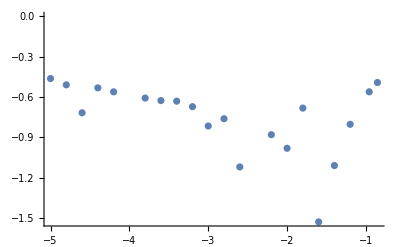
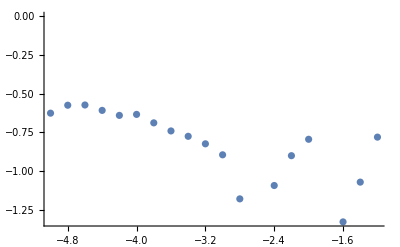
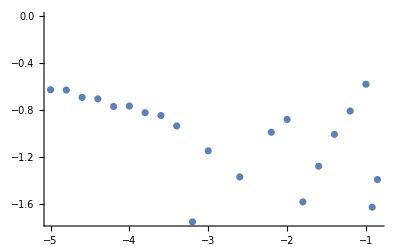
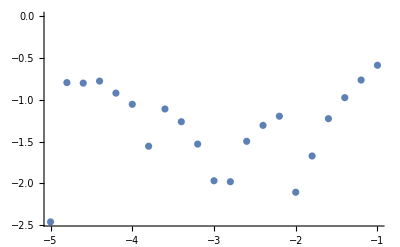
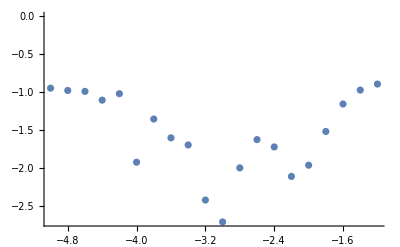
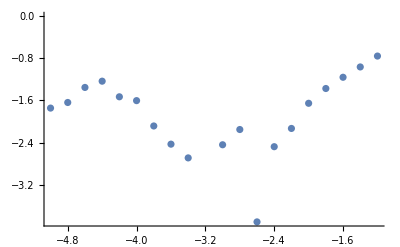

```mathematica
Table[ListPlot[Table[{Log10[Tlist[[i]]],Log10[G[[j,i]]]},{i,Length[Tlist]}]],{j,Length[plist]}]
```

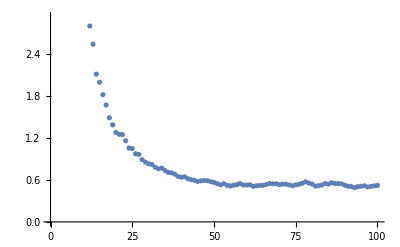

```mathematica
ListPlot[Table[datasets[[6,10]][[3,i]][[1]],{i,1,100}]]
```

```mathematica
|
```